```mathematica
(*Improved Quantum-Like International Interaction Model*)(*This model implements quantum-like mathematical formalism for international interactions with two interconnected games:crisis game and demands game.Main improvements:1. Unified parameter handling and consistent function signatures 2. Added numerical safeguards and error handling 3. Improved convergence monitoring and documentation 4. Clarified phase difference relationships 5. Added consistency checks for probabilities 6. Enhanced optimization strategy*)(* =====CRISIS GAME AMPLITUDE FUNCTIONS=====*)(*Player 1's amplitude for fighting after Player 2 fights*)aF1afterF2[U1War_,U1Cap1_,λ_,θ1a_]:=Module[{numerator,denominator,amplitude},numerator=E^(λ U1War);
denominator=E^(λ U1War)+E^(λ U1Cap1);
amplitude=Sqrt[numerator/denominator]*E^(I Re[θ1a]);
amplitude];

(*Player 1's amplitude for not fighting after Player 2 fights*)
aNF1afterF2[U1War_,U1Cap1_,λ_,θ1a_]:=Module[{numerator,denominator,amplitude},numerator=E^(λ U1Cap1);
denominator=E^(λ U1War)+E^(λ U1Cap1);
amplitude=Sqrt[numerator/denominator]*E^(I Re[θ1a]);
amplitude];

(*Player 1's amplitude for fighting after Player 2 doesn't fight*)
aF1afterNF2[U1Cap2_,U1Nego_,λ_,θ1b_]:=Module[{numerator,denominator,amplitude},numerator=E^(λ U1Cap2);
denominator=E^(λ U1Cap2)+E^(λ U1Nego);
amplitude=Sqrt[numerator/denominator]*E^(I Re[θ1b]);
amplitude];

(*Player 1's amplitude for not fighting after Player 2 doesn't fight*)
aNF1afterNF2[U1Cap2_,U1Nego_,λ_,θ1b_]:=Module[{numerator,denominator,amplitude},numerator=E^(λ U1Nego);
denominator=E^(λ U1Cap2)+E^(λ U1Nego);
amplitude=Sqrt[numerator/denominator]*E^(I Re[θ1b]);
amplitude];

(*Player 2's amplitude for fighting after Player 1 fights*)
aF2afterF1[U2War_,U2Cap2_,λ_,θ2a_]:=Module[{numerator,denominator,amplitude},numerator=E^(λ U2War);
denominator=E^(λ U2War)+E^(λ U2Cap2);
amplitude=Sqrt[numerator/denominator]*E^(I Re[θ2a]);
amplitude];

(*Player 2's amplitude for not fighting after Player 1 fights*)
aNF2afterF1[U2War_,U2Cap2_,λ_,θ2a_]:=Module[{numerator,denominator,amplitude},numerator=E^(λ U2Cap2);
denominator=E^(λ U2War)+E^(λ U2Cap2);
amplitude=Sqrt[numerator/denominator]*E^(I Re[θ2a]);
amplitude];

(*Player 2's amplitude for fighting after Player 1 doesn't fight*)
aF2afterNF1[U2Cap1_,U2Nego_,λ_,θ2b_]:=Module[{numerator,denominator,amplitude},numerator=E^(λ U2Cap1);
denominator=E^(λ U2Cap1)+E^(λ U2Nego);
amplitude=Sqrt[numerator/denominator]*E^(I Re[θ2b]);
amplitude];

(*Player 2's amplitude for not fighting after Player 1 doesn't fight*)
aNF2afterNF1[U2Cap1_,U2Nego_,λ_,θ2b_]:=Module[{numerator,denominator,amplitude},numerator=E^(λ U2Nego);
denominator=E^(λ U2Cap1)+E^(λ U2Nego);
amplitude=Sqrt[numerator/denominator]*E^(I Re[θ2b]);
amplitude];

(* =====CRISIS GAME PROBABILITY FUNCTIONS=====*)

(*Combined amplitude for Player 1 fighting*)
aF1[pF2norm_,aF1afterF2_,aF1afterNF2_]:=(Sqrt[pF2norm]*aF1afterF2)+(Sqrt[1-pF2norm]*aF1afterNF2);

(*Probability of Player 1 fighting*)
pF1[aF1_]:=aF1*Conjugate[aF1];

(*Combined amplitude for Player 1 not fighting*)
aNF1[pF2norm_,aNF1afterF2_,aNF1afterNF2_]:=(Sqrt[pF2norm]*aNF1afterF2)+(Sqrt[1-pF2norm]*aNF1afterNF2);

(*Probability of Player 1 not fighting*)
pNF1[aNF1_]:=aNF1*Conjugate[aNF1];

(*Normalized probability of Player 1 fighting*)
pF1norm[pF1_,pNF1_]:=Module[{denominator=pF1+pNF1},If[denominator==0.,0.5,pF1/denominator] (*Avoid division by zero*)];

(*Normalized probability of Player 1 not fighting*)
pNF1norm[pF1_,pNF1_]:=Module[{denominator=pF1+pNF1},If[denominator==0.,0.5,pNF1/denominator] (*Avoid division by zero*)];

(*Combined amplitude for Player 2 fighting*)
aF2[pF1norm_,aF2afterF1_,aF2afterNF1_]:=(Sqrt[pF1norm]*aF2afterF1)+(Sqrt[1-pF1norm]*aF2afterNF1);

(*Probability of Player 2 fighting*)
pF2[aF2_]:=aF2*Conjugate[aF2];

(*Combined amplitude for Player 2 not fighting*)
aNF2[pF1norm_,aNF2afterF1_,aNF2afterNF1_]:=(Sqrt[pF1norm]*aNF2afterF1)+(Sqrt[1-pF1norm]*aNF2afterNF1);

(*Probability of Player 2 not fighting*)
pNF2[aNF2_]:=aNF2*Conjugate[aNF2];

(*Normalized probability of Player 2 fighting*)
pF2norm[pF2_,pNF2_]:=Module[{denominator=pF2+pNF2},If[denominator==0.,0.5,pF2/denominator] (*Avoid division by zero*)];

(*Normalized probability of Player 2 not fighting*)
pNF2norm[pF2_,pNF2_]:=Module[{denominator=pF2+pNF2},If[denominator==0.,0.5,pNF2/denominator] (*Avoid division by zero*)];

(* =====DEMANDS GAME AMPLITUDE FUNCTIONS=====*)

(*Player 1's amplitude for demanding after Player 2 demands*)
aD1afterD2[U1Cris_,U1Acq1_,λ_,θ3a_]:=Module[{numerator,denominator,amplitude},numerator=E^(λ U1Cris);
denominator=E^(λ U1Cris)+E^(λ U1Acq1);
amplitude=Sqrt[numerator/denominator]*E^(I Re[θ3a]);
amplitude];

(*Player 1's amplitude for not demanding after Player 2 demands*)
aND1afterD2[U1Cris_,U1Acq1_,λ_,θ3a_]:=Module[{numerator,denominator,amplitude},numerator=E^(λ U1Acq1);
denominator=E^(λ U1Cris)+E^(λ U1Acq1);
amplitude=Sqrt[numerator/denominator]*E^(I Re[θ3a]);
amplitude];

(*Player 1's amplitude for demanding after Player 2 doesn't demand*)
aD1afterND2[U1Acq2_,U1SQ_,λ_,θ3b_]:=Module[{numerator,denominator,amplitude},numerator=E^(λ U1Acq2);
denominator=E^(λ U1Acq2)+E^(λ U1SQ);
amplitude=Sqrt[numerator/denominator]*E^(I Re[θ3b]);
amplitude];

(*Player 1's amplitude for not demanding after Player 2 doesn't demand*)
aND1afterND2[U1Acq2_,U1SQ_,λ_,θ3b_]:=Module[{numerator,denominator,amplitude},numerator=E^(λ U1SQ);
denominator=E^(λ U1Acq2)+E^(λ U1SQ);
amplitude=Sqrt[numerator/denominator]*E^(I Re[θ3b]);
amplitude];

(*Player 2's amplitude for demanding after Player 1 demands*)
aD2afterD1[U2Cris_,U2Acq2_,λ_,θ4a_]:=Module[{numerator,denominator,amplitude},numerator=E^(λ U2Cris);
denominator=E^(λ U2Cris)+E^(λ U2Acq2);
amplitude=Sqrt[numerator/denominator]*E^(I Re[θ4a]);
amplitude];

(*Player 2's amplitude for not demanding after Player 1 demands*)
aND2afterD1[U2Cris_,U2Acq2_,λ_,θ4a_]:=Module[{numerator,denominator,amplitude},numerator=E^(λ U2Acq2);
denominator=E^(λ U2Cris)+E^(λ U2Acq2);
amplitude=Sqrt[numerator/denominator]*E^(I Re[θ4a]);
amplitude];

(*Player 2's amplitude for demanding after Player 1 doesn't demand*)
aD2afterND1[U2Acq1_,U2SQ_,λ_,θ4b_]:=Module[{numerator,denominator,amplitude},numerator=E^(λ U2Acq1);
denominator=E^(λ U2Acq1)+E^(λ U2SQ);
amplitude=Sqrt[numerator/denominator]*E^(I Re[θ4b]);
amplitude];

(*Player 2's amplitude for not demanding after Player 1 doesn't demand*)
aND2afterND1[U2Acq1_,U2SQ_,λ_,θ4b_]:=Module[{numerator,denominator,amplitude},numerator=E^(λ U2SQ);
denominator=E^(λ U2Acq1)+E^(λ U2SQ);
amplitude=Sqrt[numerator/denominator]*E^(I Re[θ4b]);
amplitude];

(* =====DEMANDS GAME PROBABILITY FUNCTIONS=====*)

(*Combined amplitude for Player 1 demanding*)
aD1[pD2norm_,aD1afterD2_,aD1afterND2_]:=(Sqrt[pD2norm]*aD1afterD2)+(Sqrt[1-pD2norm]*aD1afterND2);

(*Probability of Player 1 demanding*)
pD1[aD1_]:=aD1*Conjugate[aD1];

(*Combined amplitude for Player 1 not demanding*)
aND1[pD2norm_,aND1afterD2_,aND1afterND2_]:=(Sqrt[pD2norm]*aND1afterD2)+(Sqrt[1-pD2norm]*aND1afterND2);

(*Probability of Player 1 not demanding*)
pND1[aND1_]:=aND1*Conjugate[aND1];

(*Normalized probability of Player 1 demanding*)
pD1norm[pD1_,pND1_]:=Module[{denominator=pD1+pND1},If[denominator==0.,0.5,pD1/denominator] (*Avoid division by zero*)];

(*Normalized probability of Player 1 not demanding*)
pND1norm[pD1_,pND1_]:=Module[{denominator=pD1+pND1},If[denominator==0.,0.5,pND1/denominator] (*Avoid division by zero*)];

(*Combined amplitude for Player 2 demanding*)
aD2[pD1norm_,aD2afterD1_,aD2afterND1_]:=(Sqrt[pD1norm]*aD2afterD1)+(Sqrt[1-pD1norm]*aD2afterND1);

(*Probability of Player 2 demanding*)
pD2[aD2_]:=aD2*Conjugate[aD2];

(*Combined amplitude for Player 2 not demanding*)
aND2[pD1norm_,aND2afterD1_,aND2afterND1_]:=(Sqrt[pD1norm]*aND2afterD1)+(Sqrt[1-pD1norm]*aND2afterND1);

(*Probability of Player 2 not demanding*)
pND2[aND2_]:=aND2*Conjugate[aND2];

(*Normalized probability of Player 2 demanding*)
pD2norm[pD2_,pND2_]:=Module[{denominator=pD2+pND2},If[denominator==0.,0.5,pD2/denominator] (*Avoid division by zero*)];

(*Normalized probability of Player 2 not demanding*)
pND2norm[pD2_,pND2_]:=Module[{denominator=pD2+pND2},If[denominator==0.,0.5,pND2/denominator] (*Avoid division by zero*)];

(* =====EQUILIBRIUM FINDING FUNCTIONS=====*)

(*
FindCrisisEquilibrium:
  Finds the equilibrium probabilities for the crisis game given utility values and phase differences between quantum states.
Parameters:
	 -u1War,u1Cap1,u1Cap2,u1Nego:Player 1's utilities for different outcomes
	-u2War,u2Cap2,u2Cap1,u2Nego:Player 2's utilities for different outcomes
	-lambda:Decision parameter controlling rationality (higher=more rational)
	-deltaTheta1,deltaTheta2:Phase differences for Players 1 and 2
	-maxIter:Maximum number of iterations for convergence
	-tolerance:Convergence threshold
  -verbose:Whether to record detailed iteration history
*)

FindCrisisEquilibrium[u1War_,u1Cap1_,u1Cap2_,u1Nego_,u2War_,
				      u2Cap2_,u2Cap1_,u2Nego_,
				      lambda_,deltaTheta1_,deltaTheta2_,
				      maxIter_:100,tolerance_:10^-6,
				      verbose_:False]:=
Module[{
pF1normCurrent=0.5,
pF2normCurrent=0.5,
pF1normNext,
pF2normNext,
a1F2,a1NF2,a1F1,a1NF1,p1F1,p1NF1,
a2F1,a2NF1,a2F2,a2NF2,p2F2,p2NF2,
theta1a,theta1b,theta2a,theta2b,
pWar,pCap2,pCap1,pNego,
iter=0,converged=False,
iterationHistory={},
totalProb},

(*Set phase differences*)
theta1a=deltaTheta1/2;
theta1b=-deltaTheta1/2;
theta2a=deltaTheta2/2;
theta2b=-deltaTheta2/2;

(*Initial probabilities*)
pWar=Re[pF1normCurrent*pF2normCurrent];
pCap2=Re[pF1normCurrent*(1-pF2normCurrent)];
pCap1=Re[(1-pF1normCurrent)*pF2normCurrent];
pNego=Re[(1-pF1normCurrent)*(1-pF2normCurrent)];

(*Keep a log for debugging purposes*)
If[verbose,
AppendTo[iterationHistory,
<|
"Iteration"->0,
"pF1"->Re[pF1normCurrent],
"pF2"->Re[pF2normCurrent],
"theta1a"->theta1a,
"theta1b"->theta1b,
"deltaTheta1"->deltaTheta1,
"theta2a"->theta2a,
"theta2b"->theta2b,
"deltaTheta2"->deltaTheta2,
"pWar"->Re[pWar],
"pCap2"->Re[pCap2],
"pCap1"->Re[pCap1],
"pNego"->Re[pNego],
"TotalProb"->pWar+pCap2+pCap1+pNego
|>
]
];

While[iter<maxIter&&!converged,

(*Calculate amplitudes for player 1*)
a1F2=aF1afterF2[u1War,u1Cap1,lambda,theta1a];
a1NF2=aNF1afterF2[u1War,u1Cap1,lambda,theta1a];
a1F1=aF1[pF2normCurrent,a1F2,aF1afterNF2[u1Cap2,u1Nego,lambda,theta1b]];
a1NF1=aNF1[pF2normCurrent,a1NF2,aNF1afterNF2[u1Cap2,u1Nego,lambda,theta1b]];
p1F1=pF1[a1F1];
p1NF1=pNF1[a1NF1];
pF1normNext=pF1norm[p1F1,p1NF1];

(*Calculate amplitudes for player 2*)
a2F1=aF2afterF1[u2War,u2Cap2,lambda,theta2a];
a2NF1=aNF2afterF1[u2War,u2Cap2,lambda,theta2a];
a2F2=aF2[pF1normCurrent,a2F1,aF2afterNF1[u2Cap1,u2Nego,lambda,theta2b]];
a2NF2=aNF2[pF1normCurrent,a2NF1,aNF2afterNF1[u2Cap1,u2Nego,lambda,theta2b]];
p2F2=pF2[a2F2];
p2NF2=pNF2[a2NF2];
pF2normNext=pF2norm[p2F2,p2NF2];

(*Calculate outcome probabilities*)
pWar=Re[pF1normCurrent*pF2normCurrent];
pCap2=Re[pF1normCurrent*(1-pF2normCurrent)];
pCap1=Re[(1-pF1normCurrent)*pF2normCurrent];
pNego=Re[(1-pF1normCurrent)*(1-pF2normCurrent)];

(*Check total probability for consistency*)
totalProb=pWar+pCap2+pCap1+pNego;
If[Abs[totalProb-1.0]>10^-10,
Print["Warning: Total probability differs from 1.0: ",totalProb];
];

(*Calculate convergence before updating values*)
converged=
Abs[pF1normNext-pF1normCurrent]<tolerance&&
Abs[pF2normNext-pF2normCurrent]<tolerance;

(*Track iteration if verbose*)
If[verbose,
AppendTo[iterationHistory,
<|
"Iteration"->iter,
"pF1"->Re[pF1normCurrent],
"pF2"->Re[pF2normCurrent],
"theta1a"->theta1a,
"theta1b"->theta1b,
"deltaTheta1"->deltaTheta1,
"theta2a"->theta2a,
"theta2b"->theta2b,
"deltaTheta2"->deltaTheta2,
"DeltapF1"->Abs[pF1normNext-pF1normCurrent],
"DeltapF2"->Abs[pF2normNext-pF2normCurrent],
"pWar"->pWar,
"pCap2"->pCap2,
"pCap1"->pCap1,
"pNego"->pNego,
"TotalProb"->totalProb|>
]
];

(*Update for next iteration*)
pF1normCurrent=Re[pF1normNext];
pF2normCurrent=Re[pF2normNext];
iter++;];

(*Return equilibrium probabilities and outcomes*)
<|
"Converged"->converged,
"Iterations"->iter,
"pF1"->Re[pF1normCurrent],
	"pF2"->Re[pF2normCurrent],
	"pWar"->pWar,
	"pCap2"->pCap2,
	"pCap1"->pCap1,
	"pNego"->pNego,
	"TotalProb"->totalProb,
	"IterationHistory"->If[verbose,iterationHistory,Null]
|>
];

(*FindFullEquilibrium:Finds the equilibrium for the full game (demands+crisis) given utility values and phase differences.Parameters:-u1War,u1Cap1,u1Cap2,u1Nego,u1SQ,u1Acq1,u1Acq2:Player 1's utilities-u2War,u2Cap2,u2Cap1,u2Nego,u2SQ,u2Acq1,u2Acq2:Player 2's utilities-lambda:Decision parameter-deltaTheta1,deltaTheta2:Phase differences for crisis game-deltaTheta3,deltaTheta4:Phase differences for demands game-maxIter:Maximum iterations-tolerance:Convergence threshold-verbose:Detailed logging*)
FindFullEquilibrium[u1War_,u1Cap1_,u1Cap2_,u1Nego_,u1SQ_,u1Acq1_,u1Acq2_,u2War_,u2Cap2_,u2Cap1_,u2Nego_,u2SQ_,u2Acq1_,u2Acq2_,lambda_,deltaTheta1_,deltaTheta2_,deltaTheta3_,deltaTheta4_,maxIter_:100,tolerance_:10^-6,verbose_:False]:=Module[{crisisEq,u1Cris,u2Cris,pD1normCurrent=0.5,pD2normCurrent=0.5,pD1normNext,pD2normNext,a1D2,a1ND2,a1D1,a1ND1,p1D1,p1ND1,a2D1,a2ND1,a2D2,a2ND2,p2D2,p2ND2,crisisPWar,crisisPCap1,crisisPCap2,crisisPNego,theta3a,theta3b,theta4a,theta4b,pCrisis,pAcq2,pAcq1,pSQ,totalProb,iter=0,converged=False,iterationHistory={}},(*Set phase differences for demands game*)theta3a=deltaTheta3/2;
theta3b=-deltaTheta3/2;
theta4a=deltaTheta4/2;
theta4b=-deltaTheta4/2;
(*First find crisis game equilibrium*)crisisEq=FindCrisisEquilibrium[u1War,u1Cap1,u1Cap2,u1Nego,u2War,u2Cap2,u2Cap1,u2Nego,lambda,deltaTheta1,deltaTheta2,maxIter,tolerance,verbose];
(*Check if crisis game converged*)If[!crisisEq["Converged"],If[verbose,Print["Warning: Crisis game did not converge."]];];
(*Extract the individual probability values*)crisisPWar=crisisEq["pWar"];
crisisPCap1=crisisEq["pCap1"];
crisisPCap2=crisisEq["pCap2"];
crisisPNego=crisisEq["pNego"];
(*Calculate expected crisis utilities*)u1Cris=crisisPWar*u1War+crisisPCap2*u1Cap2+crisisPCap1*u1Cap1+crisisPNego*u1Nego;
u2Cris=crisisPWar*u2War+crisisPCap2*u2Cap2+crisisPCap1*u2Cap1+crisisPNego*u2Nego;
(*Handle extreme utility values with numerical safeguards*)If[Abs[u1Cris]>100||Abs[u2Cris]>100,If[verbose,Print["Warning: Very high crisis utilities may cause numerical instability"]];];
(*Initialize demand game probabilities*)pCrisis=Re[pD1normCurrent*pD2normCurrent];
pAcq2=Re[pD1normCurrent*(1-pD2normCurrent)];
pAcq1=Re[(1-pD1normCurrent)*pD2normCurrent];
pSQ=Re[(1-pD1normCurrent)*(1-pD2normCurrent)];
totalProb=pCrisis+pAcq2+pAcq1+pSQ;
(*Record initial state if verbose*)If[verbose,AppendTo[iterationHistory,<|"Iteration"->0,"pD1"->Re[pD1normCurrent],"pD2"->Re[pD2normCurrent],"theta3a"->theta3a,"theta3b"->theta3b,"deltaTheta3"->deltaTheta3,"theta4a"->theta4a,"theta4b"->theta4b,"deltaTheta4"->deltaTheta4,"pCrisis"->pCrisis,"pAcq2"->pAcq2,"pAcq1"->pAcq1,"pSQ"->pSQ,"TotalProb"->totalProb|>]];
(*Now find demands game equilibrium*)While[iter<maxIter&&!converged,(*Calculate amplitudes for player 1*)a1D2=aD1afterD2[u1Cris,u1Acq1,lambda,theta3a];
a1ND2=aND1afterD2[u1Cris,u1Acq1,lambda,theta3a];
a1D1=aD1[pD2normCurrent,a1D2,aD1afterND2[u1Acq2,u1SQ,lambda,theta3b]];
a1ND1=aND1[pD2normCurrent,a1ND2,aND1afterND2[u1Acq2,u1SQ,lambda,theta3b]];
p1D1=pD1[a1D1];
p1ND1=pND1[a1ND1];
pD1normNext=pD1norm[p1D1,p1ND1];
(*Calculate amplitudes for player 2*)a2D1=aD2afterD1[u2Cris,u2Acq2,lambda,theta4a];
a2ND1=aND2afterD1[u2Cris,u2Acq2,lambda,theta4a];
a2D2=aD2[pD1normCurrent,a2D1,aD2afterND1[u2Acq1,u2SQ,lambda,theta4b]];
a2ND2=aND2[pD1normCurrent,a2ND1,aND2afterND1[u2Acq1,u2SQ,lambda,theta4b]];
p2D2=pD2[a2D2];
p2ND2=pND2[a2ND2];
pD2normNext=pD2norm[p2D2,p2ND2];
(*Update outcome probabilities*)pCrisis=Re[pD1normCurrent*pD2normCurrent];
pAcq2=Re[pD1normCurrent*(1-pD2normCurrent)];
pAcq1=Re[(1-pD1normCurrent)*pD2normCurrent];
pSQ=Re[(1-pD1normCurrent)*(1-pD2normCurrent)];
totalProb=pCrisis+pAcq2+pAcq1+pSQ;
(*Check for numerical issues*)If[Abs[totalProb-1.0]>10^-10,If[verbose,Print["Warning: Total probability in demands game differs from 1.0: ",totalProb]];];
(*Check convergence*)converged=Abs[pD1normNext-pD1normCurrent]<tolerance&&Abs[pD2normNext-pD2normCurrent]<tolerance;
(*Track iteration if verbose*)If[verbose,AppendTo[iterationHistory,<|"Iteration"->iter,"pD1"->Re[pD1normCurrent],"pD2"->Re[pD2normCurrent],"theta3a"->theta3a,"theta3b"->theta3b,"deltaTheta3"->deltaTheta3,"theta4a"->theta4a,"theta4b"->theta4b,"deltaTheta4"->deltaTheta4,"DeltapD1"->Abs[pD1normNext-pD1normCurrent],"DeltapD2"->Abs[pD2normNext-pD2normCurrent],"pCrisis"->pCrisis,"pAcq2"->pAcq2,"pAcq1"->pAcq1,"pSQ"->pSQ,"TotalProb"->totalProb|>]];
(*Update for next iteration*)pD1normCurrent=Re[pD1normNext];
pD2normCurrent=Re[pD2normNext];
iter++;];
(*Return full equilibrium probabilities and outcomes*)<|"CrisisEquilibrium"-><|"pWar"->crisisPWar,"pCap1"->crisisPCap1,"pCap2"->crisisPCap2,"pNego"->crisisPNego,"pF1"->crisisEq["pF1"],"pF2"->crisisEq["pF2"],"Converged"->crisisEq["Converged"],"Iterations"->crisisEq["Iterations"],"TotalProb"->crisisEq["TotalProb"]|>,"DemandsConverged"->converged,"DemandsIterations"->iter,"pD1"->Re[pD1normCurrent],"pD2"->Re[pD2normCurrent],"pCrisis"->pCrisis,"pAcq2"->pAcq2,"pAcq1"->pAcq1,"pSQ"->pSQ,"TotalProb"->totalProb,"ExpectedUtility1"->pCrisis*u1Cris+pAcq2*u1Acq2+pAcq1*u1Acq1+pSQ*u1SQ,"ExpectedUtility2"->pCrisis*u2Cris+pAcq2*u2Acq2+pAcq1*u2Acq1+pSQ*u2SQ,"DemandsIterationHistory"->If[verbose,iterationHistory,Null]|>];

(*FindOptimalPhases:Uses a grid search to find the optimal phase differences that maximize the log-likelihood of observing the empirical outcome data.Parameters:-dataSet:Dataset containing utility values and ground truth outcomes-lambda:Decision parameter-phaseGridSize:Number of grid points for phase search (controls precision)-optimizationMethod:"GridSearch" or "RandomSampling"-numRandomSamples:Number of random phase combinations to test*)
FindOptimalPhases[dataSet_,lambda_,phaseGridSize_:10,optimizationMethod_:"GridSearch",numRandomSamples_:100]:=Module[{phaseValues,bestFit=-Infinity,bestPhases,currentFit,results,deltaTheta1,deltaTheta2,deltaTheta3,deltaTheta4,safeLikelihood,numToTest,rand01,statusCounter},(*Create grid of phase values*)phaseValues=Table[N[2 Pi*i/phaseGridSize],{i,0,phaseGridSize-1}];
(*Initialize best phases*)bestPhases={};
(*Determine method and number of tests*)If[optimizationMethod=="GridSearch",(*Grid search-test all combinations of 4 phases*)numToTest=phaseGridSize^4;
If[numToTest>10000,Print["Warning: Grid search will test ",numToTest," combinations. This may take a long time."];];
(*For each combination of phases*)statusCounter=0;
Do[(*Update progress every 5%*)statusCounter++;
If[Mod[statusCounter,Max[1,Round[numToTest/20]]]==0,Print["Progress: ",Round[100.0*statusCounter/numToTest],"% complete"];];
(*Get equilibrium for all cases in dataset with these phase parameters*)results=Table[With[{row=dataSet[[i]]},FindFullEquilibrium[row["U1War"],row["U1Cap1"],row["U1Cap2"],row["U1Nego"],row["U1SQ"],row["U1Acq1"],row["U1Acq2"],row["U2War"],row["U2Cap2"],row["U2Cap1"],row["U2Nego"],row["U2SQ"],row["U2Acq1"],row["U2Acq2"],lambda,deltaTheta1,deltaTheta2,deltaTheta3,deltaTheta4]],{i,Length[dataSet]}];
(*Calculate fit using log-likelihood with numerical safeguards*)currentFit=Sum[With[{row=dataSet[[i]],result=results[[i]]},safeLikelihood=Which[row["groundtruth"]=="War",Log[Max[10^-10,result["CrisisEquilibrium"]["pWar"]]],row["groundtruth"]=="Cap1",Log[Max[10^-10,result["CrisisEquilibrium"]["pCap1"]]],row["groundtruth"]=="Cap2",Log[Max[10^-10,result["CrisisEquilibrium"]["pCap2"]]],row["groundtruth"]=="Nego",Log[Max[10^-10,result["CrisisEquilibrium"]["pNego"]]],row["groundtruth"]=="SQ",Log[Max[10^-10,result["pSQ"]]],row["groundtruth"]=="Acq1",Log[Max[10^-10,result["pAcq1"]]],row["groundtruth"]=="Acq2",Log[Max[10^-10,result["pAcq2"]]],True,0];
safeLikelihood],{i,Length[dataSet]}];
(*Update best fit*)If[currentFit>bestFit,bestFit=currentFit;
bestPhases={deltaTheta1,deltaTheta2,deltaTheta3,deltaTheta4};
Print["New best fit found: ",bestFit," with phases: ",bestPhases];],{deltaTheta1,phaseValues},{deltaTheta2,phaseValues},{deltaTheta3,phaseValues},{deltaTheta4,phaseValues}],(*Random sampling strategy*)Print["Using random sampling strategy with ",numRandomSamples," samples"];
Do[(*Randomly sample phase differences*)deltaTheta1=RandomReal[{0,2 Pi}];
deltaTheta2=RandomReal[{0,2 Pi}];
deltaTheta3=RandomReal[{0,2 Pi}];
deltaTheta4=RandomReal[{0,2 Pi}];
(*Report progress*)If[Mod[i,Max[1,Round[numRandomSamples/10]]]==0,Print["Progress: ",Round[100.0*i/numRandomSamples],"% complete"];];
(*Get equilibrium for all cases in dataset with these random phases*)results=Table[With[{row=dataSet[[j]]},FindFullEquilibrium[row["U1War"],row["U1Cap1"],row["U1Cap2"],row["U1Nego"],row["U1SQ"],row["U1Acq1"],row["U1Acq2"],row["U2War"],row["U2Cap2"],row["U2Cap1"],row["U2Nego"],row["U2SQ"],row["U2Acq1"],row["U2Acq2"],lambda,deltaTheta1,deltaTheta2,deltaTheta3,deltaTheta4]],{j,Length[dataSet]}];
(*Calculate fit using log-likelihood with numerical safeguards*)currentFit=Sum[With[{row=dataSet[[j]],result=results[[j]]},safeLikelihood=Which[row["groundtruth"]=="War",Log[Max[10^-10,result["CrisisEquilibrium"]["pWar"]]],row["groundtruth"]=="Cap1",Log[Max[10^-10,result["CrisisEquilibrium"]["pCap1"]]],row["groundtruth"]=="Cap2",Log[Max[10^-10,result["CrisisEquilibrium"]["pCap2"]]],row["groundtruth"]=="Nego",Log[Max[10^-10,result["CrisisEquilibrium"]["pNego"]]],row["groundtruth"]=="SQ",Log[Max[10^-10,result["pSQ"]]],row["groundtruth"]=="Acq1",Log[Max[10^-10,result["pAcq1"]]],row["groundtruth"]=="Acq2",Log[Max[10^-10,result["pAcq2"]]],True,0];
safeLikelihood],{j,Length[dataSet]}];
(*Update best fit*)If[currentFit>bestFit,bestFit=currentFit;
bestPhases={deltaTheta1,deltaTheta2,deltaTheta3,deltaTheta4};
Print["New best fit found: ",bestFit," with phases: ",bestPhases];],{i,1,numRandomSamples}]];
(*Return best phases and fit*)<|"BestPhases"->bestPhases,"LogLikelihood"->bestFit,"Lambda"->lambda,"Method"->optimizationMethod|>];

(* =====DATA PREPARATION FUNCTIONS=====*)

(*PrepareDataset:Transforms raw data into the format needed for model analysis*)
PrepareDataset[dataset_]:=Table[<|"Agent1"->dataset[i,"Agent1"],"Agent2"->dataset[i,"Agent2"],"U1War"->(dataset[i,"wrTu1wr1"]+dataset[i,"wrTu1wr2"])/2,"U1Cap1"->dataset[i,"wrTu1cp1"],"U1Cap2"->dataset[i,"wrTu1cp2"],"U1Nego"->dataset[i,"wrTu1neg"],"U1SQ"->dataset[i,"wrTu1sq"],"U1Acq1"->dataset[i,"wrTu1ac1"],"U1Acq2"->dataset[i,"wrTu1ac2"],"U2War"->(dataset[i,"wrTu2wr1"]+dataset[i,"wrTu2wr2"])/2,"U2Cap1"->dataset[i,"wrTu2cp1"],"U2Cap2"->dataset[i,"wrTu2cp2"],"U2Nego"->dataset[i,"wrTu2neg"],"U2SQ"->dataset[i,"wrTu2sq"],"U2Acq1"->dataset[i,"wrTu2ac1"],"U2Acq2"->dataset[i,"wrTu2ac2"],"groundtruth"->dataset[i,"groundtruth"]|>,{i,Length[dataset]}];

(* =====VISUALIZATION FUNCTIONS=====*)

(*PlotCrisisConvergence:Visualizes the convergence of crisis game probabilities*)
PlotCrisisConvergence[history_]:=Module[{playerPlot,outcomePlot,convergencePlot,historyTable},(*Player fight probabilities*)playerPlot=ListPlot[{Table[{i,history[[i+1,"pF1"]]},{i,0,Length[history]-1}],Table[{i,history[[i+1,"pF2"]]},{i,0,Length[history]-1}]},PlotLegends->{"Player 1","Player 2"},AxesLabel->{"Iteration","Probability"},PlotLabel->"Convergence of Fight Probabilities",Joined->True,Mesh->All,PlotMarkers->Automatic,GridLines->Automatic,PlotRange->{0,1}];
(*Outcome probabilities*)outcomePlot=ListPlot[{Table[{i,history[[i+1,"pWar"]]},{i,0,Length[history]-1}],Table[{i,history[[i+1,"pCap2"]]},{i,0,Length[history]-1}],Table[{i,history[[i+1,"pCap1"]]},{i,0,Length[history]-1}],Table[{i,history[[i+1,"pNego"]]},{i,0,Length[history]-1}]},PlotLegends->{"pWar","pCap2","pCap1","pNego"},AxesLabel->{"Iteration","Probability"},PlotLabel->"Convergence of Probabilities in Crisis Game",Joined->True,Mesh->All,PlotMarkers->Automatic,GridLines->Automatic,PlotRange->{0,1}];
(*Convergence rate*)If[Length[history]>1,convergencePlot=ListLogPlot[{Table[{i,history[[i+1,"DeltapF1"]]},{i,1,Length[history]-1}],Table[{i,history[[i+1,"DeltapF2"]]},{i,1,Length[history]-1}]},PlotLegends->{"Player 1","Player 2"},AxesLabel->{"Iteration","Log(Δp)"},PlotLabel->"Convergence Rate",Joined->True,GridLines->Automatic],convergencePlot=Graphics[{},PlotLabel->"Insufficient data for convergence plot"]];
(*Iteration table*)If[Length[history]>1,historyTable=Grid[{{"Iteration","pF1","pF2","DeltapF1","DeltapF2","theta1a","theta1b","theta2a","theta2b","deltaTheta1","deltaTheta2"}}~Join~Table[{history[[i,"Iteration"]],NumberForm[history[[i,"pF1"]],{4,4}],NumberForm[history[[i,"pF2"]],{4,4}],If[i>1,NumberForm[history[[i,"DeltapF1"]],{4,4}],"-"],If[i>1,NumberForm[history[[i,"DeltapF2"]],{4,4}],"-"],NumberForm[history[[i,"theta1a"]],{4,4}],NumberForm[history[[i,"theta1b"]],{4,4}],NumberForm[history[[i,"theta2a"]],{4,4}],NumberForm[history[[i,"theta2b"]],{4,4}],NumberForm[history[[i,"deltaTheta1"]],{4,4}],NumberForm[history[[i,"deltaTheta2"]],{4,4}]},{i,1,Min[Length[history],10]}],Frame->All,Alignment->Center,Background->{None,{LightGray,None}}],historyTable=Grid[{{"No iteration data available"}}]];
(*Return all visualizations*){playerPlot,outcomePlot,convergencePlot,historyTable}];

(*PlotDemandsConvergence:Visualizes the convergence of demands game probabilities*)
PlotDemandsConvergence[history_]:=Module[{playerPlot,outcomePlot,convergencePlot,historyTable},(*Player demand probabilities*)playerPlot=ListPlot[{Table[{i,history[[i+1,"pD1"]]},{i,0,Length[history]-1}],Table[{i,history[[i+1,"pD2"]]},{i,0,Length[history]-1}]},PlotLegends->{"Player 1","Player 2"},AxesLabel->{"Iteration","Probability"},PlotLabel->"Convergence of Demand Probabilities",Joined->True,Mesh->All,PlotMarkers->Automatic,GridLines->Automatic,PlotRange->{0,1}];
(*Outcome probabilities*)outcomePlot=ListPlot[{Table[{i,history[[i+1,"pCrisis"]]},{i,0,Length[history]-1}],Table[{i,history[[i+1,"pAcq2"]]},{i,0,Length[history]-1}],Table[{i,history[[i+1,"pAcq1"]]},{i,0,Length[history]-1}],Table[{i,history[[i+1,"pSQ"]]},{i,0,Length[history]-1}]},PlotLegends->{"pCrisis","pAcq2","pAcq1","pSQ"},AxesLabel->{"Iteration","Probability"},PlotLabel->"Convergence of Probabilities in Demands Game",Joined->True,Mesh->All,PlotMarkers->Automatic,GridLines->Automatic,PlotRange->{0,1}];
(*Convergence rate*)If[Length[history]>1,convergencePlot=ListLogPlot[{Table[{i,history[[i+1,"DeltapD1"]]},{i,1,Length[history]-1}],Table[{i,history[[i+1,"DeltapD2"]]},{i,1,Length[history]-1}]},PlotLegends->{"Player 1","Player 2"},AxesLabel->{"Iteration","Log(Δp)"},PlotLabel->"Demand Game Convergence Rate",Joined->True,GridLines->Automatic],convergencePlot=Graphics[{},PlotLabel->"Insufficient data for convergence plot"]];
(*Iteration table*)If[Length[history]>1,historyTable=Grid[{{"Iteration","pD1","pD2","DeltapD1","DeltapD2","theta3a","theta3b","theta4a","theta4b","deltaTheta3","deltaTheta4"}}~Join~Table[{history[[i,"Iteration"]],NumberForm[history[[i,"pD1"]],{4,4}],NumberForm[history[[i,"pD2"]],{4,4}],If[i>1,NumberForm[history[[i,"DeltapD1"]],{4,4}],"-"],If[i>1,NumberForm[history[[i,"DeltapD2"]],{4,4}],"-"],NumberForm[history[[i,"theta3a"]],{4,4}],NumberForm[history[[i,"theta3b"]],{4,4}],NumberForm[history[[i,"theta4a"]],{4,4}],NumberForm[history[[i,"theta4b"]],{4,4}],NumberForm[history[[i,"deltaTheta3"]],{4,4}],NumberForm[history[[i,"deltaTheta4"]],{4,4}]},{i,1,Min[Length[history],10]}],Frame->All,Alignment->Center,Background->{None,{LightGray,None}}],historyTable=Grid[{{"No iteration data available"}}]];
(*Return all visualizations*){playerPlot,outcomePlot,convergencePlot,historyTable}];

(*Create outcome probability summary table*)
CreateSummaryTable[fullResult_]:=Module[{crisisEq=fullResult["CrisisEquilibrium"]},Grid[{{"Game Stage","Outcome","Probability"},{"Crisis Game","War",crisisEq["pWar"]},{"Crisis Game","Capitulation 1",crisisEq["pCap1"]},{"Crisis Game","Capitulation 2",crisisEq["pCap2"]},{"Crisis Game","Negotiation",crisisEq["pNego"]},{"Demands Game","Crisis",fullResult["pCrisis"]},{"Demands Game","Acquiescence 1",fullResult["pAcq1"]},{"Demands Game","Acquiescence 2",fullResult["pAcq2"]},{"Demands Game","Status Quo",fullResult["pSQ"]}},Frame->All,Alignment->{Left,Left,Right},Background->{{LightGray,None},{LightGray,None,LightGray,None,LightGray,None,LightGray,None,LightGray}}]];
```

```mathematica
data=Import["C:\\Users\\cmore\\Documents\\Github\\quantum_international_interaction_game\\Norm_Form\\first_dataset_with_SQ.csv","CSV","HeaderLines"->1];
dataset=Dataset[Association@@@(Rule@@@Transpose[{{"Agent1","Agent2","wrTu1sq","wrTu1ac1","wrTu1ac2","wrTu1neg","wrTu1cp1","wrTu1cp2","wrTu1wr1","wrTu1wr2","wrTu2sq","wrTu2ac2","wrTu2ac1","wrTu2neg","wrTu2cp2","wrTu2cp1","wrTu2wr2","wrTu2wr1","groundtruth"},#}]&/@data)];
```

```mathematica
preparedData = PrepareDataset[dataset];
```

```mathematica
sampleCase=preparedData[[1]];
```

```mathematica
crisisResult=FindCrisisEquilibrium[sampleCase["U1War"],sampleCase["U1Cap1"],sampleCase["U1Cap2"],sampleCase["U1Nego"],sampleCase["U2War"],sampleCase["U2Cap2"],sampleCase["U2Cap1"],sampleCase["U2Nego"],1.0,Pi,3Pi/2,100,0.000001,True];
```

```mathematica
crisisConvergenceViz = PlotCrisisConvergence[crisisResult["IterationHistory"]];
```

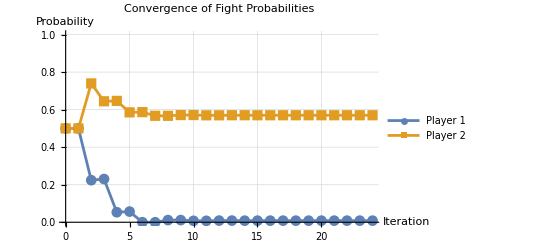

```mathematica
crisisConvergenceViz[[1]]
```

```mathematica
fullResult=FindFullEquilibrium[sampleCase["U1War"],sampleCase["U1Cap1"],sampleCase["U1Cap2"],sampleCase["U1Nego"],sampleCase["U1SQ"],sampleCase["U1Acq1"],sampleCase["U1Acq2"],sampleCase["U2War"],sampleCase["U2Cap2"],sampleCase["U2Cap1"],sampleCase["U2Nego"],sampleCase["U2SQ"],sampleCase["U2Acq1"],sampleCase["U2Acq2"],1.0,Pi/2,Pi/3,Pi/4,Pi/6,100,0.000001,True];
```

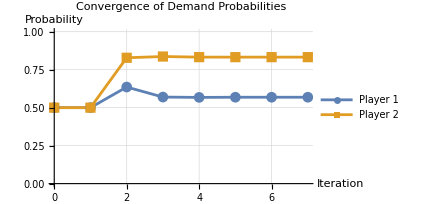
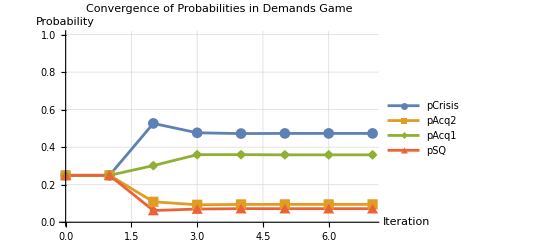
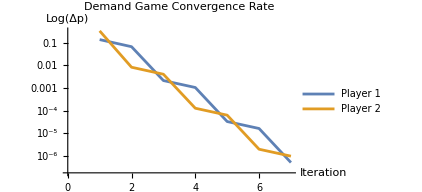
{-Graphics-,-Graphics-,-Graphics-,Iteration | pD1 | pD2 | DeltapD1 | DeltapD2 | theta3a | theta3b | theta4a | theta4b | deltaTheta3 | deltaTheta4
0 | 0.5000 | 0.5000 | - | - | π/8 | -π/8 | π/12 | -π/12 | π/4 | π/6
0 | 0.5000 | 0.5000 | 0.1357 | 0.3283 | π/8 | -π/8 | π/12 | -π/12 | π/4 | π/6
1 | 0.6357 | 0.8283 | 0.0660 | 0.0082 | π/8 | -π/8 | π/12 | -π/12 | π/4 | π/6
2 | 0.5696 | 0.8366 | 0.0021 | 0.0040 | π/8 | -π/8 | π/12 | -π/12 | π/4 | π/6
3 | 0.5675 | 0.8325 | 0.0011 | 0.0001 | π/8 | -π/8 | π/12 | -π/12 | π/4 | π/6
4 | 0.5686 | 0.8324 | 0.0000 | 0.0001 | π/8 | -π/8 | π/12 | -π/12 | π/4 | π/6
5 | 0.5686 | 0.8325 | 0.0000 | 2.0170×10^-6 | π/8 | -π/8 | π/12 | -π/12 | π/4 | π/6
6 | 0.5686 | 0.8325 | 5.2270×10^-7 | 9.9670×10^-7 | π/8 | -π/8 | π/12 | -π/12 | π/4 | π/6}

Game Stage | Outcome | Probability
Crisis Game | War | 0.542951
Crisis Game | Capitulation 1 | 0.254563
Crisis Game | Capitulation 2 | 0.137853
Crisis Game | Negotiation | 0.0646325
Demands Game | Crisis | 0.47332
Demands Game | Acquiescence 1 | 0.359144
Demands Game | Acquiescence 2 | 0.0952569
Demands Game | Status Quo | 0.0722788

```mathematica
PlotDemandsConvergence[fullResult["DemandsIterationHistory"]]
CreateSummaryTable[fullResult]
```

```mathematica
FindOptimalPhases[preparedData[[1;;750]],1.0,100,"RandomSampling",50];
```

Using random sampling strategy with 50 samples

New best fit found: -1201.04 with phases: {5.96071,1.70963,4.26813,3.3349}

New best fit found: -1160.86 with phases: {1.738,2.01448,4.43681,0.628927}

New best fit found: -1143.58 with phases: {6.21981,2.39125,3.09212,2.45837}

Progress: 10% complete

New best fit found: -1087.51 with phases: {5.40753,3.86705,3.4529,0.0936089}

Progress: 20% complete

New best fit found: -1076.41 with phases: {4.96434,4.24574,2.50969,2.69186}

New best fit found: -1064.15 with phases: {5.865,3.41362,3.91339,3.75478}

Progress: 30% complete

Progress: 40% complete

Progress: 50% complete

Progress: 60% complete

Progress: 70% complete

Progress: 80% complete

Progress: 90% complete

Progress: 100% complete

```mathematica
(*  lambda= 1 *)
```

```mathematica
FindOptimalPhases[preparedData[[1;;750]],1.0,100,"RandomSampling",500];
```

Using random sampling strategy with 500 samples

New best fit found: -1159.79 with phases: {4.47918,5.52068,3.27322,2.01773}

New best fit found: -1098.72 with phases: {2.56147,5.88123,3.33403,5.08545}

New best fit found: -1097.87 with phases: {4.13204,2.84232,2.59384,5.73504}

New best fit found: -1049.57 with phases: {6.24227,3.3463,2.50648,3.83301}

Progress: 10% complete

New best fit found: -1032.99 with phases: {4.08072,2.21468,2.75984,3.92378}

New best fit found: -1029. with phases: {2.03116,5.11154,2.82156,2.5798}

Progress: 20% complete

Progress: 30% complete

Progress: 40% complete

Progress: 50% complete

New best fit found: -1001.51 with phases: {5.89148,3.16683,2.85238,3.59381}

Progress: 60% complete

Progress: 70% complete

Progress: 80% complete

Progress: 90% complete

Progress: 100% complete